```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\HAL-master\\process\\theo.txt", "Table"];
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<101, i++,cleanData=Append[cleanData,data[[i]][[4]]] ]
```

```mathematica
cleanData;
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<51, i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData;
```

```mathematica
For[i=1,i<=100, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData;
```

```mathematica
probDensFunc[x_]:=N[probabilityData[[x+1,2]]/100]
```

```mathematica
probDensFunc[0]
```

0.07

http://math.bme.hu/~nandori/Virtual_lab/stat/expect/Generating.pdf

```mathematica
probGenFunc[z_]:=Sum[probDensFunc[n]*(z^n),{n,0,50}]
```

```mathematica
probGenFunc[0.01]
```

0.0705071

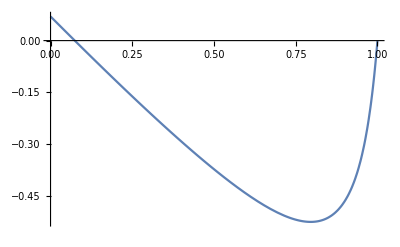

```mathematica
Plot[probGenFunc[t]-t,{t,0,1}]
```